# Rotating star

Author : Martin Horvat, June 2016

## Potential of the rotating star

```mathematica
Clear[Omega];
Omega[x_,y_,z_,omega_]:=1/Sqrt[x^2+y^2+z^2]+1/2 omega^2(x^2+y^2)
```

```mathematica
Clear[DOmega];
DOmega[x_,y_,z_,omega_]=D[Omega[x,y,z,omega],{{x,y,z}}]
```

{omega^2 x-x/((x^2+y^2+z^2)^(3/2)),omega^2 y-y/((x^2+y^2+z^2)^(3/2)),-z/((x^2+y^2+z^2)^(3/2))}

```mathematica
Simplify[DOmega[0,0,1/Omega0,omega],Omega0>0]
```

{0,0,-Omega0^2}

## Plots

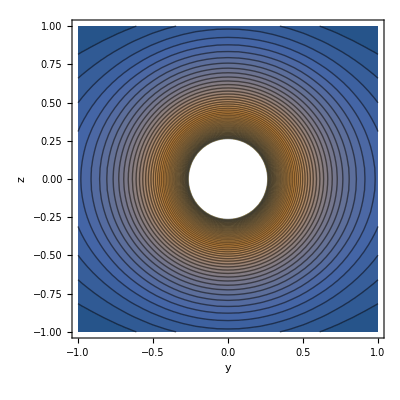

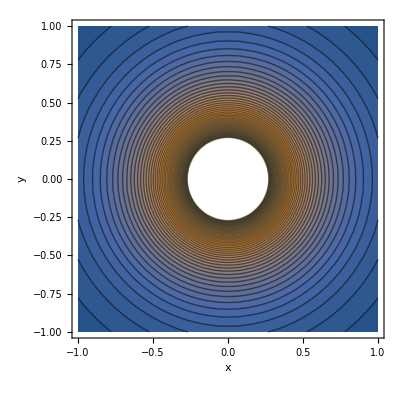

```mathematica
ContourPlot[Omega[0,y,z,0.5],{y,-1,1},{z,-1,1},Contours->50,AxesLabel->{"y","z"}]
ContourPlot[Omega[x,y,0,0.5],{x,-1,1},{y,-1,1},Contours->50,AxesLabel->{"x","y"}]
```

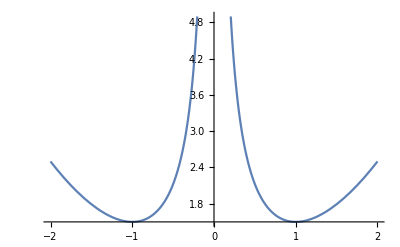

```mathematica
Plot[Omega[x,0,0,1],{x,-2,2}]
```

## Volume and area as integrals along rho^2 -- not good weakly singular

Using 
z = v/Omega, 
rho = u/Omega, 
b = omega^2/(2 Omega^2)

```mathematica
v[s_,b_]:= Sqrt[-s(1-b*s)^2+1]/(1-b*s);
dvds[s_,b_]=-FullSimplify[D[v[s,b],s]]
```

-(-1+b (2+s (3+b s (-3+b s))))/(2 (-1+b s)^2 √(1-s (-1+b s)^2))

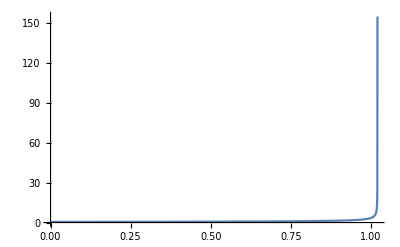

```mathematica
Block[{s0,u0,b},
b=0.01;
u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];
s0=u0*u0;
Plot[dvds[s,b],{s,0,s0*0.99999},PlotRange->All]
]
```

```mathematica
Block[{b,omega, Omega0,s,s0,u0,u},
omega=1;
Omega0=2;
b= 1/2 omega^2/Omega0^3;

u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];

s0=u0*u0;

Print[u0," ",s0];

NIntegrate[{4Pi/Omega0^2*Sqrt[s*dvds[s,b]^2+1/4],2Pi/Omega0^3*s*dvds[s,b]},{s,0,s0}]
]
```

1.07838 1.1629

{3.46918,0.606626}

```mathematica
Block[{b,omega, Omega0,s,s0,u0,u},

b= 1/2  0.2;

u0=Min[Select[u/.NSolve[b*u^3-u+1==0,u,Reals],#>0&]];

s0=u0*u0;

Print[u0," ",s0];

NIntegrate[{Sqrt[s*dvds[s,b]^2+1/4],s dvds[s,b]},{s,0,s0}]
]
```

1.15347 1.33049

{1.20285,0.874144}

## Series inversion

```mathematica
(* Implementation of one of the simpler algorithms for series reversion,due to Henry Thacher.*)
Clear[MyInverseSeries];
MyInverseSeries[a_]:=Module[{n=Length[a],b=a/a[[1]],c,i,j,k},
Do[
Do[
c[i,j+1]=Sum[c[k,1]c[i-k,j],{k,1,i-j}],
{j,i-1,1,-1}
];
c[i,1]=Boole[i==1]-Sum[b[[j]] c[i,j],{j,2,i}],
{i,n}
];
Table[c[i,1],{i,n}]/a[[1]]^Range[n]
]
```

```mathematica
a=Rest[CoefficientList[Series[2ArcSin[x],{x,0,20}],x]];
MyInverseSeries[a]
```

{1/2,0,-1/48,0,1/3840,0,-1/645120,0,1/185794560,0,-1/81749606400,0,1/51011754393600,0,-1/42849873690624000,0,1/46620662575398912000,0,-1/63777066403145711616000}

```mathematica
Rest[CoefficientList[InverseSeries[Series[2ArcSin[x],{x,0,20}]],x]]
```

{1/2,0,-1/48,0,1/3840,0,-1/645120,0,1/185794560,0,-1/81749606400,0,1/51011754393600,0,-1/42849873690624000,0,1/46620662575398912000,0,-1/63777066403145711616000}

## Shape via expansion : u(v)

Working with
	1= 1/Sqrt[u^2 + v^2] + b u^2	
or using s=u^2 and t = v^2
	1= 1/Sqrt[s + t] + b s	b=1/2 β
	
We are basically searching for s(t), where we know s(1) = 0.

Let us try to do t=(1-x)^2 and find s(x) for x[0,1]. 

Note that b < b_crit = 4/27 , β< β_c=8/27=0.296296

```mathematica
SolS[x_,β_]:=Min[s/.Solve[1==1/Sqrt[s+(1-x)^2]+1/2 β s,s]]
```

Max::nord: Invalid comparison with -109.493+3.55271×10^-15 ⅈ attempted.

Max::nord: Invalid comparison with -89.4659-7.10543×10^-15 ⅈ attempted.

Max::nord: Invalid comparison with 20.027-1.42109×10^-14 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

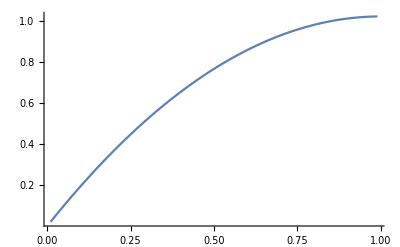

```mathematica
Plot[Re[SolS[x,0.02]],{x,0.01,0.99},PlotRange->All]
```

```mathematica
Normal[Simplify[Series[(1-1/Sqrt[s+(1-x)^2])/s,{x,0,3},{s,0,3}],0<x<1]]
```

1/2-(3 s)/8+(5 s^2)/16-(35 s^3)/128+(3/2-1/s-(15 s)/8+(35 s^2)/16-(315 s^3)/128) x+(3-1/s-(45 s)/8+(35 s^2)/4-(1575 s^3)/128) x^2+(5-1/s-(105 s)/8+(105 s^2)/4-(5775 s^3)/128) x^3

```mathematica
n=20;
m=10;
DS=Simplify[Table[D[1-Sqrt[(1-1/2β s)^-2-s],{s,i}]/i!,{i,n}]/.s->0];
iDS=MyInverseSeries[DS];
```

```mathematica
(*Sana[x_,β_]=Normal[Simplify[InverseSeries[Simplify[Series[1-Sqrt[(1-1/2β s)^-2-s],{s,0,n}]],x]]];*)
(*Sana[x_,β_]=Normal[InverseSeries[DS.(s^Range[n])+O[s]^(n+1),x]];*)
Sana[x_,β_]=iDS.(x^Range[Length[iDS]]);
```

```mathematica
N[Sana[1/10,1/Pi]-Sana1[1/10,1/Pi]]
```

0.

Max::nord: Invalid comparison with -23.9793+2.66454×10^-15 ⅈ attempted.

Max::nord: Invalid comparison with -14.9741-7.10543×10^-15 ⅈ attempted.

Max::nord: Invalid comparison with 9.00518-1.06581×10^-14 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

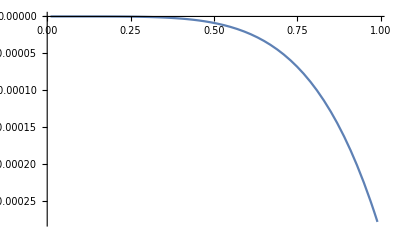

```mathematica
Plot[Sana[x,0.1]/Re[SolS[x,0.1]]-1,{x,0.01,0.99},PlotRange->All]
```

```mathematica
Vana[β_]=Integrate[Normal[Series[3/2*Sana[x,β],{β,0,10}]],{x,0,1}]
```

1+β+(8 β^2)/5+(22 β^3)/7+(104 β^4)/15+(544 β^5)/33+(41344 β^6)/1001+(6992 β^7)/65+(443327 β^8)/1536+(25377 β^9)/32+(175839795 β^10)/78848

```mathematica
Aana[β_]=Integrate[Normal[Series[Sqrt[Sana[x,β]+D[Sana[x,β],x]^2/4],{β,0,10}]],{x,0,1}]
```

1+(2 β)/3+β^2+(68 β^3)/35+(151 β^4)/35+(2402 β^5)/231+(397729 β^6)/15015+(3163304 β^7)/45045+(12537575201 β^8)/65345280+(95198998129 β^9)/177365760+(11442340778207 β^10)/7449361920

```mathematica
Vana[0.1]
```

0.746705

```mathematica
Aana[0.1]
```

1.07918

```mathematica
CForm[HornerForm[Sum[a[i]t^i,{i,0,10}],t]]
```

a(0) + t*(a(1) + t*(a(2) + t*(a(3) + t*(a(4) + t*(a(5) + t*(a(6) + t*(a(7) + t*(a(8) + t*(a(9) + t*a(10))))))))))

```mathematica
SetOptions[InputNotebook[],PrintPrecision->16]
```

```mathematica
CForm/@N[CoefficientList[Vana[β],β]]
```

{1.,1.,1.6,3.142857142857143,6.933333333333334,16.484848484848484,41.302697302697304,107.56923076923077,288.6243489583333,793.03125,2230.111036424513}

```mathematica
CForm/@N[CoefficientList[D[Vana[β],β],β]]
```

```mathematica
CForm/@N[CoefficientList[Aana[β],β]]
```

{1.,0.6666666666666666,1.,1.9428571428571428,4.314285714285714,10.398268398268398,26.48877788877789,70.22541902541903,191.8665770657039,536.7383091809828,1536.0162254282043}

```mathematica
CForm[HornerForm[D[Sum[a[i]t^i,{i,0,10}],t],t]]
```

a(1) + t*(2*a(2) + t*(3*a(3) + t*(4*a(4) + t*(5*a(5) + t*(6*a(6) + t*(7*a(7) + t*(8*a(8) + t*(9*a(9) + 10*t*a(10)))))))))

## Shape via integration

### Using t = v^2

```mathematica
A=s'[t]/.FullSimplify[Solve[D[1/Sqrt[s[t]+t]+b s[t],t]==0,s'[t]]][[1]]
```

1/(-1+2 b t √(t+s[t])+2 b s[t] √(t+s[t]))

```mathematica
Simplify[A/.√(t+s[t])->q]/.{t->1,s[t]->0,q->1,b->0.1}
```

-1.25

```mathematica
D[1/Sqrt[s[t]+t]+b s[t],t]==0
```

b s'[t]-(1+s'[t])/(2 (t+s[t])^(3/2))==0

### Using v = Omega0 z

```mathematica
s'[v]/.FullSimplify[Solve[D[1/Sqrt[s[v]+v^2]+b s[v],v]==0,s'[v]]][[1]]
```

(2 v)/(-1+2 b v^2 √(v^2+s[v])+2 b s[v] √(v^2+s[v]))

## Hessian

```mathematica
H=D[D[Omega[x,y,z,omega],{{x,y,z}}]/.omega^2->w2,{{x,y,z}}]
```

{{w2+(3 x^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2)),(3 x y)/((x^2+y^2+z^2)^(5/2)),(3 x z)/((x^2+y^2+z^2)^(5/2))},{(3 x y)/((x^2+y^2+z^2)^(5/2)),w2+(3 y^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2)),(3 y z)/((x^2+y^2+z^2)^(5/2))},{(3 x z)/((x^2+y^2+z^2)^(5/2)),(3 y z)/((x^2+y^2+z^2)^(5/2)),(3 z^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2))}}

```mathematica
Ha=Simplify[Expand[FullSimplify[-H/.{x^2+y^2+z^2->f^-2},f>0]]/.{f^5->f5,f^3->f3,x^2->x2,y^2->y2,z^2->z2}]
```

{{f3-w2-3 f5 x2,-3 f5 x y,-3 f5 x z},{-3 f5 x y,f3-w2-3 f5 y2,-3 f5 y z},{-3 f5 x z,-3 f5 y z,f3-3 f5 z2}}

```mathematica
CForm[Ha[[1,1]]]
```

f3 - w2 - 3*f5*x2

```mathematica
CForm[Ha[[1,2]]]
```

-3*f5*x*y

```mathematica
CForm[Ha[[1,3]]]
```

-3*f5*x*z

```mathematica
CForm[Ha[[2,2]]]
```

f3 - w2 - 3*f5*y2

```mathematica
CForm[Ha[[2,3]]]
```

-3*f5*y*z

```mathematica
CForm[Ha[[3,3]]]
```

f3 - 3*f5*z2